# Examples “returned to store”

### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

## “Kaitlyn Delong” <delongk@southern.edu>:

### 5898765100

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs589=FromReducedRankIndex[5898765100]
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>




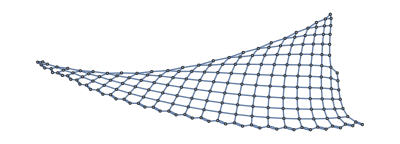
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss589=SSS[rs589[["RuleSet"]], "B",200, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->25, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
Short[Sort@sss589[["Net"]],6]
```

{1→2,1→2,1→5,2→3,3→4,3→4,3→5,4→6,5→8,6→7,6→7,6→8,7→9,8→11,8→12,9→10,9→10,9→11,10→13,11→12,11→15,12→16,13→14,13→14,«326»,181→195,182→183,182→196,183→184,183→197,184→185,184→198,185→186,185→199,186→187,186→200,187→188,188→189,189→190,190→191,191→192,193→194,193→194,193→195,195→196,196→197,197→198,198→199,199→200}

```mathematica
nds589=ToNetDifferenceSets[sss589[["Net"]]]
```

{{1,1,4},{1},{1,1,2},{2},{3},{1,1,2},{2},{3,4},{1,1,2},{3},{1,4},{4},{1,1,2},{3},{1,4},{4,5},{1,1,2},{4},{1,5},{1,5},{5},{1,1,2},{4},{1,5},{1,5},{5,6},{1,1,2},{5},{1,6},{1,6},{1,6},{6},{1,1,2},{5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{6},{1,7},{1,7},{1,7},{1,7},{7},{1,1,2},{6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{8},{1,1,2},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,1,2},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,1,2},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,1,2},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,1,2},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},{1,1,2},{12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1},{1},{1},{1},{1},{},{1,1,2},{},{1},{1},{1},{1},{1}}

```mathematica
rsl589=ReduceSetList[nds589]
```

{{1,1,4},{1},{1,1,2},€_(n$1⊨1)^2[{1+n$1}],€_(n$2⊨1)^10[{1,1,2},{1+n$2},€^(-1+n$2)[{1,2+n$2}],{2+n$2,3+n$2},{1,1,2},{2+n$2},€^n$2[{1,3+n$2}],{3+n$2}],{1,1,2},{12},€^10[{1,13}],{13,14},{1,1,2},{13},€^6[{1,14}],€^5[{1}],{},{1,1,2},{},€^5[{1}]}

Get an editable version of the most compressed part.

```mathematica
{rsl589[[5]]}/.n$2->k
```

{€_(k⊨1)^10[{1,1,2},{1+k},€^(-1+k)[{1,2+k}],{2+k,3+k},{1,1,2},{2+k},€^k[{1,3+k}],{3+k}]}

```mathematica
InputForm@{rsl589[[5]]}/.n$2->k
```

{IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, 
   -1 + k], {2 + k, 3 + k}, {1, 1, 2}, {2 + k}, 
  IndexedConcatenate[{1, 3 + k}, k], {3 + k}, {k, 1, 10}]}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, 
  -1 + k], {2 + k, 3 + k}, {1, 1, 2}, {2 + k}, 
 IndexedConcatenate[{1, 3 + k}, k], {3 + k}, {k, 0, 0}]}//ExpandAll
```

{{1,1,2},{1},{2,3},{1,1,2},{2},{3}}

That works even before k=1, so we may replace k by k-1:

```mathematica
{InputForm@rsl589[[5]]}/.n$2->k-1//InputForm
```

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 11}]}
```

{€_(k⊨1)^11[{1,1,2},{k},€^(-2+k)[{1,1+k}],{1+k,2+k},{1,1,2},{1+k},€^(-1+k)[{1,2+k}],{2+k}]}

But only some of our first “slice” of the concatenation are actually in the net:

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 2}]}//ExpandAll
```

```mathematica
{{1,1,2},{1},{2,3},{1,1,2},{2},{3},{1,1,2},{2},{3,4},{1,1,2},{3},{1,4},{4}}
```

```mathematica
Take[nds589,10]
```

```mathematica
{{1,1,4},{1},{1,1,2},{2},{3},{1,1,2},{2},{3,4},{1,1,2},{3}}
```

To fix this, start our IC with the 4^th element, moving the first 3 to the end (and reverting k->k+1):

```mathematica
IC589={IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k},
{1, 1, 2}, {k+1}, IndexedConcatenate[{1, k+2}, k-1],{k+2, k+3}, 
 {k, 1, 10}]};
IC589//ExpandAll
```

{{1,1,2},{2},{3},{1,1,2},{2},{3,4},{1,1,2},{3},{1,4},{4},{1,1,2},{3},{1,4},{4,5},{1,1,2},{4},{1,5},{1,5},{5},{1,1,2},{4},{1,5},{1,5},{5,6},{1,1,2},{5},{1,6},{1,6},{1,6},{6},{1,1,2},{5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{6},{1,7},{1,7},{1,7},{1,7},{7},{1,1,2},{6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{8},{1,1,2},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,1,2},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,1,2},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,1,2},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,1,2},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13}}

```mathematica
Length[%]
```

150

Now this matches our set list starting at its 3^rd element:

```mathematica
nds589[[3;;150+2]]==ExpandAll@IC589
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
rs589
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

Best start at 3^rd step:

```mathematica
sss589[["Evolution"]][[3]]
```

BA

```mathematica
IC589//InputForm
```

{IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, 
   -1 + k], {2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, 
   -1 + k], {2 + k, 3 + k}, {k, 1, 10}]}

```mathematica
IC589
```

{€_(k⊨1)^10[{1,1,2},{k+1},€^(k-1)[{1,k+2}],{k+2},{1,1,2},{k+1},€^(k-1)[{1,k+2}],{k+2,k+3}]}

### 5906311975

```mathematica
rs590=FromReducedRankIndex[5906311975]
```

<|Index→5906311975,QCode→32432342324233,RuleSet→{AA→BA,AB→AA,B→AAA}|>

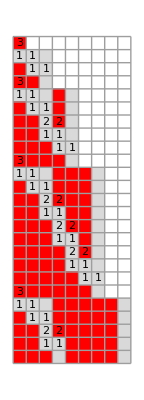
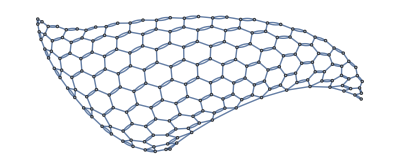
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss590=SSS[rs590[["RuleSet"]], "B",200, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->25, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
Short[Sort@sss590[["Net"]],6]
```

{1→2,1→2,1→3,2→3,2→4,3→7,3→9,4→5,4→5,4→6,5→6,5→10,6→7,6→13,7→8,7→8,8→9,8→15,9→17,9→19,10→11,10→11,10→12,11→12,11→20,«339»,183→184,184→185,185→186,185→186,186→187,187→188,187→188,188→189,189→190,189→190,190→191,191→192,191→192,192→193,193→194,193→194,194→195,195→196,195→196,196→197,197→198,197→198,198→199,199→200,199→200}

```mathematica
nds590=ToNetDifferenceSets[sss590[["Net"]]]
```

{{1,1,2},{1,2},{4,6},{1,1,2},{1,5},{1,7},{1,1},{1,7},{8,10},{1,1,2},{1,9},{1,11},{1,1},{1,11},{1,1},{1,11},{1,1},{1,11},{12,14},{1,1,2},{1,13},{1,15},{1,1},{1,15},{1,1},{1,15},{1,1},{1,15},{1,1},{1,15},{1,1},{1,15},{16,18},{1,1,2},{1,17},{1,19},{1,1},{1,19},{1,1},{1,19},{1,1},{1,19},{1,1},{1,19},{1,1},{1,19},{1,1},{1,19},{1,1},{1,19},{20,22},{1,1,2},{1,21},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{1,1},{1,23},{24,26},{1,1,2},{1,25},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{1,1},{1,27},{28,30},{1,1,2},{1,29},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{1,1},{1,31},{32,34},{1,1,2},{1,33},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{1,1},{1,35},{36},{1,1,2},{1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
rsl590=ReduceSetList[nds590]
```

{{1,1,2},{1,2},{4,6},{1,1,2},€_(n$1⊨1)^2[{1,5+2 (-1+n$1)}],{1,1},€_(n$2⊨1)^7[{1,3+4 n$2},{4 (1+n$2),2 (3+2 n$2)},{1,1,2},{1,5+4 n$2},€^(1+2 n$2)[{1,7+4 n$2},{1,1}]],{1,35},{36},{1,1,2},€^2[{1}],€^16[{1,1},{1}],{1,1}}

Get an editable version of the most compressed part.

```mathematica
{rsl590[[7]]}/.n$2->k
```

{€_(k⊨1)^7[{1,4 k+3},{4 (k+1),2 (2 k+3)},{1,1,2},{1,4 k+5},€^(2 k+1)[{1,4 k+7},{1,1}]]}

That works even before k=1, so we may replace k by 2:

```mathematica
Clear[k];
{InputForm@rsl590[[7]]}/.n$2->k-2//ExpandAll
```

Table::write: Tag Plus in -2+k is Protected.

{InputForm[{1,3+4 (-2+k)},{4 (-1+k),2 (3+2 (-2+k))},{1,1,2},{1,5+4 (-2+k)},€^(1+2 (-2+k))[{1,7+4 (-2+k)},{1,1}],-2+k,1,7]}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 11}]}
```

```mathematica
IC589={IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k},
{1, 1, 2}, {k+1}, IndexedConcatenate[{1, k+2}, k-1],{k+2, k+3}, 
 {k, 1, 10}]};
IC589//ExpandAll
```

Now this matches our set list starting at its 3^rd element:

```mathematica
nds589[[3;;150+2]]==ExpandAll@IC589
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
rs589
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

Best start at 3^rd step:

```mathematica
sss589[["Evolution"]][[3]]
```

```mathematica
IC589//InputForm
```

```mathematica
IC589
```

### 733448810021

```mathematica
rs590=FromReducedRankIndex[5906311975]
```

```mathematica
sss590=SSS[rs590[["RuleSet"]], "B",200, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->25, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
Short[Sort@sss589[["Net"]],6]
```

```mathematica
nds589=ToNetDifferenceSets[sss589[["Net"]]]
```

```mathematica
rsl589=ReduceSetList[nds589]
```

Get an editable version of the most compressed part.

```mathematica
{rsl589[[5]]}/.n$2->k
```

```mathematica
InputForm@{rsl589[[5]]}/.n$2->k
```

That works even before k=1, so we may replace k by k-1:

```mathematica
{InputForm@rsl589[[5]]}/.n$2->k-1//InputForm
```

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 11}]}
```

```mathematica
IC589={IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k},
{1, 1, 2}, {k+1}, IndexedConcatenate[{1, k+2}, k-1],{k+2, k+3}, 
 {k, 1, 10}]};
IC589//ExpandAll
```

Now this matches our set list starting at its 3^rd element:

```mathematica
nds589[[3;;150+2]]==ExpandAll@IC589
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
rs589
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

Best start at 3^rd step:

```mathematica
sss589[["Evolution"]][[3]]
```

```mathematica
IC589//InputForm
```

```mathematica
IC589
```

### 733448814971

```mathematica
rs590=FromReducedRankIndex[5906311975]
```

```mathematica
sss590=SSS[rs590[["RuleSet"]], "B",200, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->25, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
Short[Sort@sss589[["Net"]],6]
```

```mathematica
nds589=ToNetDifferenceSets[sss589[["Net"]]]
```

```mathematica
rsl589=ReduceSetList[nds589]
```

Get an editable version of the most compressed part.

```mathematica
{rsl589[[5]]}/.n$2->k
```

```mathematica
InputForm@{rsl589[[5]]}/.n$2->k
```

That works even before k=1, so we may replace k by k-1:

```mathematica
{InputForm@rsl589[[5]]}/.n$2->k-1//InputForm
```

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 11}]}
```

```mathematica
IC589={IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k},
{1, 1, 2}, {k+1}, IndexedConcatenate[{1, k+2}, k-1],{k+2, k+3}, 
 {k, 1, 10}]};
IC589//ExpandAll
```

Now this matches our set list starting at its 3^rd element:

```mathematica
nds589[[3;;150+2]]==ExpandAll@IC589
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
rs589
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

Best start at 3^rd step:

```mathematica
sss589[["Evolution"]][[3]]
```

```mathematica
IC589//InputForm
```

```mathematica
IC589
```

### ..

```mathematica
rs590=FromReducedRankIndex[5906311975]
```

```mathematica
sss590=SSS[rs590[["RuleSet"]], "B",200, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->25, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
Short[Sort@sss589[["Net"]],6]
```

```mathematica
nds589=ToNetDifferenceSets[sss589[["Net"]]]
```

```mathematica
rsl589=ReduceSetList[nds589]
```

Get an editable version of the most compressed part.

```mathematica
{rsl589[[5]]}/.n$2->k
```

```mathematica
InputForm@{rsl589[[5]]}/.n$2->k
```

That works even before k=1, so we may replace k by k-1:

```mathematica
{InputForm@rsl589[[5]]}/.n$2->k-1//InputForm
```

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 11}]}
```

```mathematica
IC589={IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k},
{1, 1, 2}, {k+1}, IndexedConcatenate[{1, k+2}, k-1],{k+2, k+3}, 
 {k, 1, 10}]};
IC589//ExpandAll
```

Now this matches our set list starting at its 3^rd element:

```mathematica
nds589[[3;;150+2]]==ExpandAll@IC589
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
rs589
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

Best start at 3^rd step:

```mathematica
sss589[["Evolution"]][[3]]
```

```mathematica
IC589//InputForm
```

```mathematica
IC589
```

### ..

```mathematica
rs590=FromReducedRankIndex[5906311975]
```

```mathematica
sss590=SSS[rs590[["RuleSet"]], "B",200, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->25, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
Short[Sort@sss589[["Net"]],6]
```

```mathematica
nds589=ToNetDifferenceSets[sss589[["Net"]]]
```

```mathematica
rsl589=ReduceSetList[nds589]
```

Get an editable version of the most compressed part.

```mathematica
{rsl589[[5]]}/.n$2->k
```

```mathematica
InputForm@{rsl589[[5]]}/.n$2->k
```

That works even before k=1, so we may replace k by k-1:

```mathematica
{InputForm@rsl589[[5]]}/.n$2->k-1//InputForm
```

```mathematica
{IndexedConcatenate[{1, 1, 2}, {k}, IndexedConcatenate[{1, 1 + k}, -2 + k], {1 + k, 2 + k}, {1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k}, {k, 1, 11}]}
```

```mathematica
IC589={IndexedConcatenate[{1, 1, 2}, {1 + k}, IndexedConcatenate[{1, 2 + k}, -1 + k], {2 + k},
{1, 1, 2}, {k+1}, IndexedConcatenate[{1, k+2}, k-1],{k+2, k+3}, 
 {k, 1, 10}]};
IC589//ExpandAll
```

Now this matches our set list starting at its 3^rd element:

```mathematica
nds589[[3;;150+2]]==ExpandAll@IC589
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
rs589
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

Best start at 3^rd step:

```mathematica
sss589[["Evolution"]][[3]]
```

```mathematica
IC589//InputForm
```

```mathematica
IC589
```